```mathematica
SetDirectory["/Users/christopher.illingworth/Documents/GitHub/IVY/Calculations/Simulations"];
```

```mathematica
ProcessIV[vals_]:=Module[{out,db},
out=1;
db=vals[[1]]-vals[[2]];
If[db>10,out=2];
Return[out];
];

ProcessIVY[vals_]:=Module[{out,db1,db2},
out=1;
db1=vals[[1]]-vals[[2]];
If[db1>10,
db2=vals[[2]]-vals[[3]];
If[db2>10,out=3,out=2];
];
Return[out];
];

ProcessIVYX[vals_]:=Module[{out,db1,db2,db3},
out=1;
db1=vals[[1]]-vals[[2]];
If[db1>10,
db2=vals[[2]]-vals[[3]];
If[db2>10,
db3=vals[[3]]-vals[[4]];
If[db3>10,
out=4,out=3
],out=2];
];
Return[out];
];

EvaluateBIC[vals_]:=If[Length[vals]==4,ProcessIVYX[vals],
If[Length[vals]==3,ProcessIVY[vals]],ProcessIV[vals]];
```

```mathematica
EvaluateBIC[bic[[1]]]
```

IVYX

290.888

56.1116

1.75201

3

```mathematica
bic[[1]]
```

{383.927,93.0388,36.9272,35.1751}

```mathematica
Basic simulations: One rate of evolution: One population
```

```mathematica
Rate 0.1
```

```mathematica
ldat=Table[Import["Rate01/Split1/Sim"<>ToString[i]<>"/Likelihoods.out","Table"],{i,1,100}];
ldat2=Table[ldat[[i,;;,-1]],{i,1,100}];
bic=Table[{Log[6]-2*ldat2[[i,1]],2*Log[6]-2*ldat2[[i,2]]},{i,1,100}];
npop=Table[EvaluateBIC[bic[[i]]],{i,1,100}];
np=Tally[npop];
(*dbic=Reverse[Sort[Table[bic[[i,1]]-bic[[i,2]],{i,1,100}]]]*)
```

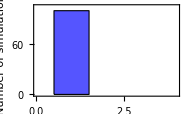

```mathematica
Show[Table[Graphics[{Lighter[Blue],EdgeForm[Black],Rectangle[{np[[i,1]]-0.5,0},{np[[i,1]]+0.5,np[[i,2]]}]}],{i,1,Length[np]}],Frame->True,AspectRatio->1/GoldenRatio,PlotRange->{{0,4},{0,105}},FrameLabel->{{"Number of simulations",None},{"Number of inferred populations","One population: Rate 0.1"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->187]
```

```mathematica
rates=Table[Import["Rate01/Split1/Sim"<>ToString[i]<>"/RatesIE.out","Table"],{i,1,100}];
rates=Table[{rates[[i,1,2]],rates[[i,2,2]],rates[[i,2,3]]},{i,1,Length[rates]}];
est=rates[[;;,1]];
interval=Table[{rates[[i,2]],rates[[i,3]]},{i,1,100}];
counts=Table[Length[Select[est,#>i&&#<=i+0.025&]],{i,0,0.3,0.025}];
bounds=rates[[;;,{2,3}]];
pbounds=Table[{{rates[[i,2]],i},{rates[[i,3]],i}},{i,1,100}];
Mean[est]
Length[Select[interval,#[[1]]<0.1&&#[[2]]>0.1&]]
```

0.101

93

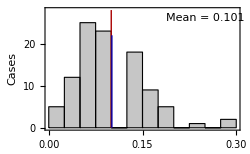

```mathematica
p1=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts[[i*40+1]]}]}],{i,0,0.275,0.025}],Graphics[{Darker[Red],Line[{{0.1,0},{0.1,28}}]}],Graphics[{Darker[Blue],Line[{{0.101,0},{0.101,22}}]}],Graphics[Text["Mean = 0.101",{0.25,26}]],Frame->True,FrameLabel->{"Rate","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
```

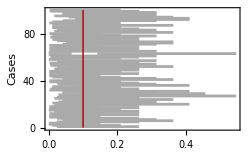

```mathematica
p2=Show[ListLinePlot[pbounds,PlotStyle->Lighter[Gray],Frame->True,ImageSize->250,FrameLabel->{"Rate","Cases"},FrameStyle->Directive[FontSize->10,Black]],Graphics[{Darker[Red],Line[{{0.1,0},{0.1,100}}]}]]
```

```mathematica
Rate 0.2
```

```mathematica
ldat=Table[Import["Rate02/Split1/Sim"<>ToString[i]<>"/Likelihoods.out","Table"],{i,1,100}];
ldat2=Table[ldat[[i,;;,-1]],{i,1,100}];
bic=Table[{Log[6]-2*ldat2[[i,1]],2*Log[6]-2*ldat2[[i,2]]},{i,1,100}];
npop=Table[EvaluateBIC[bic[[i]]],{i,1,100}];
np=Tally[npop];
Show[Table[Graphics[{Lighter[Blue],EdgeForm[Black],Rectangle[{np[[i,1]]-0.5,0},{np[[i,1]]+0.5,np[[i,2]]}]}],{i,1,Length[np]}],Frame->True,AspectRatio->1/GoldenRatio,PlotRange->{{0,4},{0,105}},FrameLabel->{{"Number of simulations",None},{"Number of inferred populations","One population: Rate 0.2"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->187]
(*dbic=Reverse[Sort[Table[bic[[i,1]]-bic[[i,2]],{i,1,100}]]]*)
```

-Graphics-

```mathematica
rates=Table[Import["Rate02/Split1/Sim"<>ToString[i]<>"/RatesIE.out","Table"],{i,1,100}];
rates=Table[{rates[[i,1,2]],rates[[i,2,2]],rates[[i,2,3]]},{i,1,Length[rates]}];
est=rates[[;;,1]];
interval=Table[{rates[[i,2]],rates[[i,3]]},{i,1,100}];
counts=Table[Length[Select[est,#>i&&#<=i+0.025&]],{i,0,0.5,0.025}];
bounds=rates[[;;,{2,3}]];
pbounds=Table[{{rates[[i,2]],i},{rates[[i,3]],i}},{i,1,100}];
Mean[est]
Length[Select[interval,#[[1]]<0.2&&#[[2]]>0.2&]]
```

0.199333

98

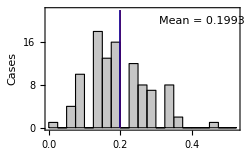

```mathematica
p1=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts[[i*40+1]]}]}],{i,0,0.5,0.025}],Graphics[{Darker[Red],Line[{{0.2,0},{0.2,22}}]}],Graphics[{Darker[Blue],Line[{{0.199333,0},{0.199333,22}}]}],Graphics[Text["Mean = 0.1993",{0.43,20}]],Frame->True,FrameLabel->{"Rate","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
```

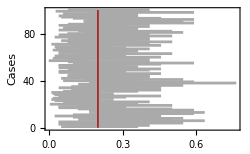

```mathematica
p2=Show[ListLinePlot[pbounds,PlotStyle->Lighter[Gray],Frame->True,ImageSize->250,FrameLabel->{"Rate","Cases"},FrameStyle->Directive[FontSize->10,Black]],Graphics[{Darker[Red],Line[{{0.2,0},{0.2,100}}]}]]
```

```mathematica
Rate 0.3
```

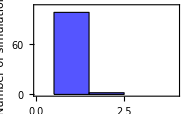

```mathematica
ldat=Table[Import["Rate03/Split1/Sim"<>ToString[i]<>"/Likelihoods.out","Table"],{i,1,100}];
ldat2=Table[ldat[[i,;;,-1]],{i,1,100}];
bic=Table[{Log[6]-2*ldat2[[i,1]],2*Log[6]-2*ldat2[[i,2]]},{i,1,100}];
npop=Table[EvaluateBIC[bic[[i]]],{i,1,100}];
np=Tally[npop];
Show[Table[Graphics[{Lighter[Blue],EdgeForm[Black],Rectangle[{np[[i,1]]-0.5,0},{np[[i,1]]+0.5,np[[i,2]]}]}],{i,1,Length[np]}],Frame->True,AspectRatio->1/GoldenRatio,PlotRange->{{0,4},{0,105}},FrameLabel->{{"Number of simulations",None},{"Number of inferred populations","One population: Rate 0.3"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->187]
(*dbic=Reverse[Sort[Table[bic[[i,1]]-bic[[i,2]],{i,1,100}]]]*)
```

```mathematica
rates=Table[Import["Rate03/Split1/Sim"<>ToString[i]<>"/RatesIE.out","Table"],{i,1,100}];
rates=Table[{rates[[i,1,2]],rates[[i,2,2]],rates[[i,2,3]]},{i,1,Length[rates]}];
est=rates[[;;,1]];
interval=Table[{rates[[i,2]],rates[[i,3]]},{i,1,100}];
counts=Table[Length[Select[est,#>i&&#<=i+0.025&]],{i,0,0.55,0.025}];
bounds=rates[[;;,{2,3}]];
pbounds=Table[{{rates[[i,2]],i},{rates[[i,3]],i}},{i,1,100}];
Mean[est]
Length[Select[interval,#[[1]]<0.3&&#[[2]]>0.3&]]
```

0.294

98

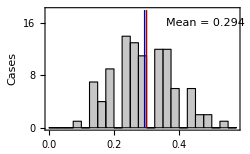

```mathematica
p1=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts[[i*40+1]]}]}],{i,0,0.55,0.025}],Graphics[{Darker[Red],Line[{{0.3,0},{0.3,18}}]}],Graphics[{Darker[Blue],Line[{{0.294,0},{0.294,18}}]}],Graphics[Text["Mean = 0.294",{0.48,16}]],Frame->True,FrameLabel->{"Rate","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
```

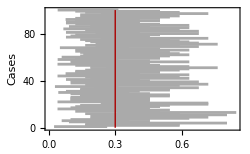

```mathematica
p2=Show[ListLinePlot[pbounds,PlotStyle->Lighter[Gray],Frame->True,ImageSize->250,FrameLabel->{"Rate","Cases"},FrameStyle->Directive[FontSize->10,Black]],Graphics[{Darker[Red],Line[{{0.3,0},{0.3,100}}]}]]
```

```mathematica
Split simulation - one rate of evolution 0.1
```

76

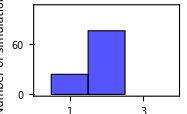

```mathematica
ldat=Table[Import["Rate01/Split2/Sim"<>ToString[i]<>"/Likelihoods.out","Table"],{i,1,100}];
ldat2=Table[ldat[[i,;;,-1]],{i,1,100}];
bic=Table[{Log[6]-2*ldat2[[i,1]],2*Log[6]-2*ldat2[[i,2]],3*Log[6]-2*ldat2[[i,2]]},{i,1,100}];
bicres=Table[EvaluateBIC[bic[[i]]],{i,1,Length[bic]}];
call1=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==1&][[;;,1]];
call2=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==2&][[;;,1]];
Length[Select[bicres,#==2&]]
npop=Table[EvaluateBIC[bic[[i]]],{i,1,100}];
np=Tally[npop];
Show[Table[Graphics[{Lighter[Blue],EdgeForm[Black],Rectangle[{np[[i,1]]-0.5,0},{np[[i,1]]+0.5,np[[i,2]]}]}],{i,1,Length[np]}],Frame->True,AspectRatio->1/GoldenRatio,PlotRange->{{0.1,3.9},{0,105}},FrameLabel->{{"Number of simulations",None},{"Number of inferred populations","Two populations: Rate 0.1 and 0.1"}},FrameTicks->{{Automatic,Automatic},{{1,2,3},Automatic}},FrameStyle->Directive[Black,FontSize->10],ImageSize->187]
(*dbic=Reverse[Sort[Table[bic[[i,1]]-bic[[i,2]],{i,1,100}]]]*)
```

```mathematica
rates=Table[Import["Rate01/Split2/Sim"<>ToString[i]<>"/RatesIE.out","Table"],{i,call1}];
Mean[rates[[;;,1,2]]]
```

0.0777777

0.0947807

0.599998

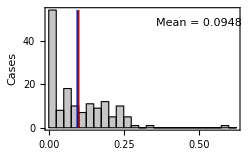

```mathematica
rates=Table[Import["Rate01/Split2/Sim"<>ToString[i]<>"/RatesVE.out","Table"],{i,call2}];
Mean[Flatten[rates[[;;,1,{1,2}]]]]
est=Flatten[rates[[;;,1,{1,2}]]];
Max[est]
counts=Table[Length[Select[est,#>i&&#<=i+0.025&]],{i,0,0.6,0.025}];
p1=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts[[i*40+1]]}]}],{i,0,0.6,0.025}],Graphics[{Darker[Red],Line[{{0.1,0},{0.1,54}}]}],Graphics[{Darker[Blue],Line[{{0.09478,0},{0.09478,54}}]}],Graphics[Text["Mean = 0.0948",{0.5,48}]],Frame->True,FrameLabel->{"Rate","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
```

```mathematica
Split simulation - two rates of evolution 0.1 and 0.2
```

93

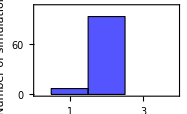

```mathematica
ldat=Table[Import["Rate0102/Split2/Sim"<>ToString[i]<>"/Likelihoods.out","Table"],{i,1,100}];
ldat2=Table[ldat[[i,;;,-1]],{i,1,100}];
bic=Table[{Log[6]-2*ldat2[[i,1]],2*Log[6]-2*ldat2[[i,2]],3*Log[6]-2*ldat2[[i,3]]},{i,1,100}];
bicres=Table[EvaluateBIC[bic[[i]]],{i,1,Length[bic]}];
call1=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==1&][[;;,1]];
call2=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==2&][[;;,1]];
Length[Select[bicres,#==2&]]
npop=Table[EvaluateBIC[bic[[i]]],{i,1,100}];
np=Tally[npop];
Show[Table[Graphics[{Lighter[Blue],EdgeForm[Black],Rectangle[{np[[i,1]]-0.5,0},{np[[i,1]]+0.5,np[[i,2]]}]}],{i,1,Length[np]}],Frame->True,AspectRatio->1/GoldenRatio,PlotRange->{{0.1,3.9},{0,105}},FrameLabel->{{"Number of simulations",None},{"Number of inferred populations","Two populations: Rate 0.1 and 0.2"}},FrameTicks->{{Automatic,Automatic},{{1,2,3},Automatic}},FrameStyle->Directive[Black,FontSize->10],ImageSize->187]
```

```mathematica
call1=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==1&][[;;,1]];
call2=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==2&][[;;,1]];
```

```mathematica
rates=Table[Import["Rate0102/Split2/Sim"<>ToString[i]<>"/RatesIE.out","Table"],{i,call1}];
Mean[rates[[;;,1,2]]]
```

0.138095

{0.0703583,0.21448}

0.466667

0.799997

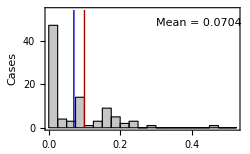

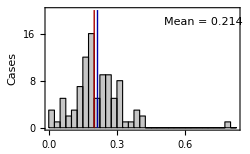

```mathematica
rates=Table[Import["Rate0102/Split2/Sim"<>ToString[i]<>"/RatesVE.out","Table"],{i,call2}];
Mean[Table[Sort[rates[[i,1,{1,2}]]],{i,1,Length[call2]}]]
est1=Table[Sort[rates[[i,1,{1,2}]]],{i,1,Length[call2]}][[;;,1]];
Max[est1]
est2=Table[Sort[rates[[i,1,{1,2}]]],{i,1,Length[call2]}][[;;,2]];
Max[est2]
counts1=Table[Length[Select[est1,#>i&&#<=i+0.025&]],{i,0,0.5,0.025}];
counts2=Table[Length[Select[est2,#>i&&#<=i+0.025&]],{i,0,0.8,0.025}];
p1=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts1[[i*40+1]]}]}],{i,0,0.5,0.025}],Graphics[{Darker[Red],Line[{{0.1,0},{0.1,54}}]}],Graphics[{Darker[Blue],Line[{{0.0704,0},{0.0704,54}}]}],Graphics[Text["Mean = 0.0704",{0.42,48}]],Frame->True,FrameLabel->{"Rate 1","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
p2=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts2[[i*40+1]]}]}],{i,0,0.8,0.025}],Graphics[{Darker[Red],Line[{{0.2,0},{0.2,20}}]}],Graphics[{Darker[Blue],Line[{{0.21448,0},{0.21448,20}}]}],Graphics[Text["Mean = 0.214",{0.68,18}]],Frame->True,FrameLabel->{"Rate 2","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
```

```mathematica
Split simulation - two rates of evolution 0.1 and 0.3
```

97

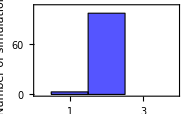

```mathematica
ldat=Table[Import["Rate0103/Split2/Sim"<>ToString[i]<>"/Likelihoods.out","Table"],{i,1,100}];
ldat2=Table[ldat[[i,;;,-1]],{i,1,100}];
bic=Table[{Log[6]-2*ldat2[[i,1]],2*Log[6]-2*ldat2[[i,2]],3*Log[6]-2*ldat2[[i,3]]},{i,1,100}];
bicres=Table[EvaluateBIC[bic[[i]]],{i,1,Length[bic]}];
call1=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==1&][[;;,1]];
call2=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==2&][[;;,1]];
Length[Select[bicres,#==2&]]
npop=Table[EvaluateBIC[bic[[i]]],{i,1,100}];
np=Tally[npop];
Show[Table[Graphics[{Lighter[Blue],EdgeForm[Black],Rectangle[{np[[i,1]]-0.5,0},{np[[i,1]]+0.5,np[[i,2]]}]}],{i,1,Length[np]}],Frame->True,AspectRatio->1/GoldenRatio,PlotRange->{{0.1,3.9},{0,105}},FrameLabel->{{"Number of simulations",None},{"Number of inferred populations","Two populations: Rate 0.1 and 0.3"}},FrameTicks->{{Automatic,Automatic},{{1,2,3},Automatic}},FrameStyle->Directive[Black,FontSize->10],ImageSize->187]
```

```mathematica
call1=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==1&][[;;,1]];
call2=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==2&][[;;,1]];
```

```mathematica
rates=Table[Import["Rate0102/Split2/Sim"<>ToString[i]<>"/RatesIE.out","Table"],{i,call1}];
Mean[rates[[;;,1,2]]]
```

0.138095

{0.0786739,0.300754}

0.366667

0.633334

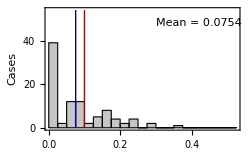

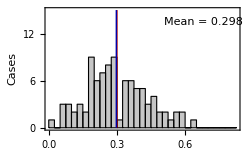

```mathematica
rates=Table[Import["Rate0103/Split2/Sim"<>ToString[i]<>"/RatesVE.out","Table"],{i,call2}];
Mean[Table[Sort[rates[[i,1,{1,2}]]],{i,1,Length[call2]}]]
est1=Table[Sort[rates[[i,1,{1,2}]]],{i,1,Length[call2]}][[;;,1]];
Max[est1]
est2=Table[Sort[rates[[i,1,{1,2}]]],{i,1,Length[call2]}][[;;,2]];
Max[est2]
counts1=Table[Length[Select[est1,#>i&&#<=i+0.025&]],{i,0,0.5,0.025}];
counts2=Table[Length[Select[est2,#>i&&#<=i+0.025&]],{i,0,0.8,0.025}];
p1=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts1[[i*40+1]]}]}],{i,0,0.5,0.025}],Graphics[{Darker[Red],Line[{{0.1,0},{0.1,54}}]}],Graphics[{Darker[Blue],Line[{{0.0754295,0},{0.0754295,54}}]}],Graphics[Text["Mean = 0.0754",{0.42,48}]],Frame->True,FrameLabel->{"Rate 1","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
p2=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts2[[i*40+1]]}]}],{i,0,0.8,0.025}],Graphics[{Darker[Red],Line[{{0.3,0},{0.3,15}}]}],Graphics[{Darker[Blue],Line[{{0.297287,0},{0.297287,15}}]}],Graphics[Text["Mean = 0.298",{0.68,13.5}]],Frame->True,FrameLabel->{"Rate 2","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
```

```mathematica
Split simulation - three rates of evolution 0.1 0.2 0.3
```

3

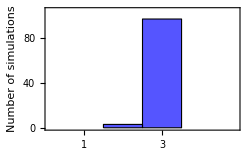

```mathematica
ldat=Table[Import["Rate010203/Split3/Sim"<>ToString[i]<>"/Likelihoods.out","Table"],{i,1,100}];
ldat2=Table[ldat[[i,;;,-1]],{i,1,100}];
bic=Table[{Log[10]-2*ldat2[[i,1]],2*Log[10]-2*ldat2[[i,2]],3*Log[10]-2*ldat2[[i,3]],4*Log[10]-2*ldat2[[i,4]]},{i,1,100}];
bicres=Table[EvaluateBIC[bic[[i]]],{i,1,Length[bic]}];
call1=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==1&][[;;,1]];
call2=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==2&][[;;,1]];
Length[Select[bicres,#==2&]]
npop=Table[EvaluateBIC[bic[[i]]],{i,1,100}];
np=Tally[npop];
Show[Table[Graphics[{Lighter[Blue],EdgeForm[Black],Rectangle[{np[[i,1]]-0.5,0},{np[[i,1]]+0.5,np[[i,2]]}]}],{i,1,Length[np]}],Frame->True,AspectRatio->1/GoldenRatio,PlotRange->{{0.1,4.9},{0,105}},FrameLabel->{{"Number of simulations",None},{"Number of inferred populations","Three populations: Rates 0.1, 0.2, 0.3"}},FrameTicks->{{Automatic,Automatic},{{1,2,3,4},Automatic}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250]
```

```mathematica
Length[call3]
```

97

```mathematica
call3=Select[Partition[Riffle[Range[100],bicres],2],#[[2]]==3&][[;;,1]];
```

{0.07575,0.176649,0.307079}

0.200003

0.400004

0.55

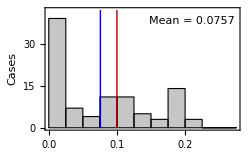

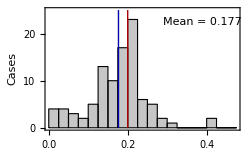

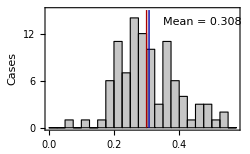

```mathematica
rates=Table[Import["Rate010203/Split3/Sim"<>ToString[i]<>"/RatesYE.out","Table"],{i,call3}];
Mean[Table[Sort[rates[[i,1,{1,2,3}]]],{i,1,Length[call3]}]]
est1=Table[Sort[rates[[i,1,{1,2,3}]]],{i,1,Length[call3]}][[;;,1]];
Max[est1]
est2=Table[Sort[rates[[i,1,{1,2,3}]]],{i,1,Length[call3]}][[;;,2]];
Max[est2]
est3=Table[Sort[rates[[i,1,{1,2,3}]]],{i,1,Length[call3]}][[;;,3]];
Max[est3]
counts1=Table[Length[Select[est1,#>i&&#<=i+0.025&]],{i,0,0.25,0.025}];
counts2=Table[Length[Select[est2,#>i&&#<=i+0.025&]],{i,0,0.45,0.025}];
counts3=Table[Length[Select[est3,#>i&&#<=i+0.025&]],{i,0,0.6,0.025}];
p1=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts1[[i*40+1]]}]}],{i,0,0.25,0.025}],Graphics[{Darker[Red],Line[{{0.1,0},{0.1,42}}]}],Graphics[{Darker[Blue],Line[{{0.0757496,0},{0.0757496,42}}]}],Graphics[{FontSize->10,Text["Mean = 0.0757",{0.21,38}]}],Frame->True,FrameLabel->{"Rate 1","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
p2=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts2[[i*40+1]]}]}],{i,0,0.45,0.025}],Graphics[{Darker[Red],Line[{{0.2,0},{0.2,25}}]}],Graphics[{Darker[Blue],Line[{{0.176655,0},{0.176655,25}}]}],Graphics[{FontSize->10,Text["Mean = 0.177",{0.39,22.5}]}],Frame->True,FrameLabel->{"Rate 2","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
p2=Show[Table[Graphics[{EdgeForm[Directive[Thin,Black]],Lighter[Lighter[Gray]],Rectangle[{i,0},{i+0.025,counts3[[i*40+1]]}]}],{i,0,0.55,0.025}],Graphics[{Darker[Red],Line[{{0.3,0},{0.3,15}}]}],Graphics[{Darker[Blue],Line[{{0.307592,0},{0.307592,15}}]}],Graphics[{FontSize->10,Text["Mean = 0.308",{0.47,13.5}]}],Frame->True,FrameLabel->{"Rate 3","Cases"},FrameStyle->Directive[FontSize->10,Black],AspectRatio->1/GoldenRatio,ImageSize->250]
```